```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

```mathematica
Clear[r] 
r = { x[t] + ( ξ0 + R θ[t] ) Cos[ϕ] , H - R θ[t] Sin[ϕ] }
```

{x[t]+Cos[ϕ] (ξ0+R θ[t]),H-R Sin[ϕ] θ[t]}

```mathematica
D[r, t]
```

{x'[t]+R Cos[ϕ] θ'[t],-R Sin[ϕ] θ'[t]}

```mathematica
D[r, t] . D[r, t]
```

R^2 Sin[ϕ]^2 θ'[t]^2+(x'[t]+R Cos[ϕ] θ'[t])^2

```mathematica
D[r, t] . D[r, t] // Expand
```

x'[t]^2+2 R Cos[ϕ] x'[t] θ'[t]+R^2 Cos[ϕ]^2 θ'[t]^2+R^2 Sin[ϕ]^2 θ'[t]^2

```mathematica
D[r, t] . D[r, t] // Expand  // Simplify
```

x'[t]^2+2 R Cos[ϕ] x'[t] θ'[t]+R^2 θ'[t]^2

```mathematica
Clear[T] 
T = 1/2 m x'[t]^2 + 1/2 M( D[r, t] . D[r, t] // Expand  // Simplify )+ 1/2(2/5 M R^2) θ'[t]^2
```

1/2 m x'[t]^2+1/5 M R^2 θ'[t]^2+1/2 M (x'[t]^2+2 R Cos[ϕ] x'[t] θ'[t]+R^2 θ'[t]^2)

```mathematica
Clear[V]
V = M g ( H - R θ[t] Sin[ϕ] )
```

g M (H-R Sin[ϕ] θ[t])

```mathematica
Clear[ℒ]
ℒ = T - V
```

-g M (H-R Sin[ϕ] θ[t])+1/2 m x'[t]^2+1/5 M R^2 θ'[t]^2+1/2 M (x'[t]^2+2 R Cos[ϕ] x'[t] θ'[t]+R^2 θ'[t]^2)

```mathematica
ℒ // pdConv
```

-g M (H-R θ(t) sin(ϕ))+1/2 m ((∂x(t))/(∂t))^2+1/5 M R^2 ((∂θ(t))/(∂t))^2+1/2 M (R^2 ((∂θ(t))/(∂t))^2+2 R cos(ϕ) (∂θ(t))/(∂t) (∂x(t))/(∂t)+((∂x(t))/(∂t))^2)

```mathematica
Clear[q]
q = { x[t] , θ[t] }
```

{x[t],θ[t]}

```mathematica
D[ D[ ℒ , D[q[[1]], t] ],t] - D[ ℒ , q[[1]] ] 
D[ D[ ℒ , D[q[[2]], t] ],t] - D[ ℒ , q[[2]] ]
```

m x''[t]+1/2 M (2 x''[t]+2 R Cos[ϕ] θ''[t])

-g M R Sin[ϕ]+2/5 M R^2 θ''[t]+1/2 M (2 R Cos[ϕ] x''[t]+2 R^2 θ''[t])

```mathematica
Table[
D[ D[ ℒ , D[q[[i]], t] ],t] - D[ ℒ , q[[i]] ] == 0 ,
{i,1,2} ] // TableForm
```

m x''[t]+1/2 M (2 x''[t]+2 R Cos[ϕ] θ''[t])==0
-g M R Sin[ϕ]+2/5 M R^2 θ''[t]+1/2 M (2 R Cos[ϕ] x''[t]+2 R^2 θ''[t])==0

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , q, t ] ;
eqs // TableForm
```

-(m+M) x''[t]-M R Cos[ϕ] θ''[t]==0
-1/5 M R (-5 g Sin[ϕ]+5 Cos[ϕ] x''[t]+7 R θ''[t])==0

```mathematica
Clear[ics]
ics = { 
x[0] == 0 ,
x'[0] == 0 ,
θ[0] == 0 ,
θ'[0] == 0 
} ;
ics // TableForm
```

x[0]==0
x'[0]==0
θ[0]==0
θ'[0]==0

```mathematica
Clear[parameters]
parameters = {
g-> 9.8 ,
m -> 100 ,
M -> 20 ,
R -> 1,
ϕ-> π/6 
} ;
parameters // TableForm
```

g→9.8
m→100
M→20
R→1
ϕ→π/6

```mathematica
eqs /. parameters // TableForm
```

-120 x''[t]-10 √3 θ''[t]==0
-4 (-24.5+5/2 √3 x''[t]+7 θ''[t])==0

```mathematica
Clear[solution]
solution = 
NDSolve[ Union[ eqs /. parameters , ics ] , q , { t, 0, 10 } ]
```

{{x[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t]}}

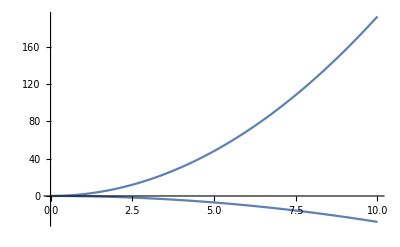

```mathematica
Plot[ q /. solution , { t, 0, 10 } ]
```

```mathematica
Exit[]
Quit[]
```